## PDFs

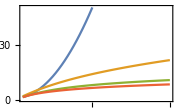

```mathematica
Plot[{
-Log[PDF[NormalDistribution[0,1],x]],
-Log[PDF[LogNormalDistribution[0,1/2],x+1]],
-Log[PDF[StudentTDistribution[0,1,3],x]],
-Log[PDF[ParetoDistribution[1,2],x+1]]
},{x,1,20},Frame->True,ImageSize->Small,
PlotLegends->"Expressions"]
```

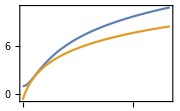

```mathematica
Plot[{
-Log[PDF[StudentTDistribution[0,1,3],x]],
-Log[PDF[ParetoDistribution[1,2],x+1]]
},{x,0,20},Frame->True,ImageSize->Small,
PlotLegends->"Expressions"]
```

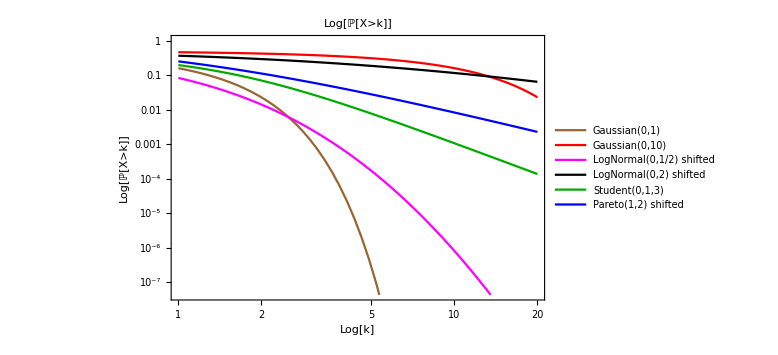

```mathematica
LogLogPlot[{
1-CDF[NormalDistribution[0,1],k],
1-CDF[NormalDistribution[0,10],k],
1-CDF[LogNormalDistribution[0,1/2],k+1],
1-CDF[LogNormalDistribution[0,2],k+1],
1-CDF[StudentTDistribution[0,1,3],k],
1-CDF[ParetoDistribution[1,2],k+1]
},{k,1,20},Frame->True,ImageSize->Large,PlotLabel->"Log[ℙ[X>k]]",FrameLabel->{"Log[k]","Log[ℙ[X>k]]"},
PlotLegends->{"Gaussian(0,1)","Gaussian(0,10)","LogNormal(0,1/2) shifted","LogNormal(0,2) shifted","Student(0,1,3)","Pareto(1,2) shifted"},
PlotStyle->{Brown,Red,Magenta,Black,Darker[Green],Blue}]
```

## Surprise

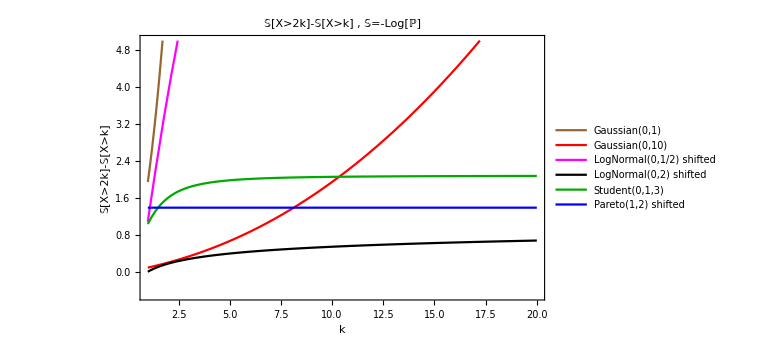

```mathematica
Plot[{
(-Log[1-CDF[NormalDistribution[0,1],2k]]+Log[1-CDF[NormalDistribution[0,1],k]]),
(-Log[1-CDF[NormalDistribution[0,10],2k]]+Log[1-CDF[NormalDistribution[0,10],k]]),
(-Log[1-CDF[LogNormalDistribution[0,1/2],2k]]+Log[1-CDF[LogNormalDistribution[0,1],k+1]]),
(-Log[1-CDF[LogNormalDistribution[0,2],2k]]+Log[1-CDF[LogNormalDistribution[0,2],k+1]]),
(-Log[1-CDF[StudentTDistribution[0,1,3],2k]]+Log[1-CDF[StudentTDistribution[0,1,3],k]]),
(-Log[1-CDF[ParetoDistribution[1,2],2(k+1)]]+Log[1-CDF[ParetoDistribution[1,2],k+1]])
},{k,1,20},Frame->True,ImageSize->Large,PlotLabel->"𝕊[X>2k]-𝕊[X>k] , 𝕊=-Log[ℙ]",FrameLabel->{"k","𝕊[X>2k]-𝕊[X>k]"},
PlotLegends->{"Gaussian(0,1)","Gaussian(0,10)","LogNormal(0,1/2) shifted","LogNormal(0,2) shifted","Student(0,1,3)","Pareto(1,2) shifted"},
PlotStyle->{Brown,Red,Magenta,Black,Darker[Green],Blue},PlotRange->{All,{-0.5,5}}]
```

## Histograms

```mathematica
fX[dist_, runs_]:=RandomVariate[dist,runs];
```

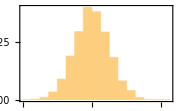

```mathematica
Histogram[fX[NormalDistribution[0,1],5000],"Knuth","PDF",Frame->True,ImageSize->Small]
```

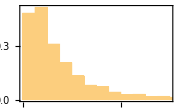

```mathematica
Histogram[fX[LogNormalDistribution[0,1],5000],"Knuth","PDF",Frame->True,ImageSize->Small]
```

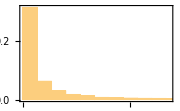

```mathematica
Histogram[fX[LogNormalDistribution[0,2],5000],"Knuth","PDF",Frame->True,ImageSize->Small]
```

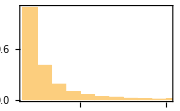

```mathematica
Histogram[fX[ParetoDistribution[1,2],5000],"Knuth","PDF",Frame->True,ImageSize->Small]
```

```mathematica
N[MapThread[inform[NormalDistribution[0,1],#1,#2]&,
{Most[{-∞,-3,-2,0,+2,+3,+∞}],Rest[{-∞,-3,-2,0,+2,+3,+∞}]}]]
```

{6.60773,3.84435,0.739715,0.739715,3.84435,6.60773}

```mathematica
fX[NormalDistribution[0,1],{5,2}]
```

{{-0.909984,0.1338},{0.444034,-0.513394},{-0.622458,0.509275},{-2.1088,-0.0130404},{0.539193,-0.279803}}

## Sums

```mathematica
fS[dist_, runs_, n_]:=Map[Accumulate,fX[dist, {runs,n}]];
```

```mathematica
fSLast[dist_, runs_, n_]:=Map[Total,fX[dist, {runs,n}]];
```

```mathematica
fS[NormalDistribution[0,1],5,3]
```

{{-0.378865,0.44401,1.00159},{-1.47889,0.0569973,1.09257},{1.70977,0.979399,0.671798},{0.655845,0.0836124,0.174931},{-0.871945,-1.92928,-1.03799}}

```mathematica
fSLast[NormalDistribution[0,1],5,30]
```

{-4.23436,7.32084,10.8116,2.29252,6.21991}

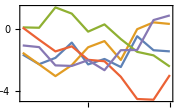

```mathematica
ListLinePlot[fS[NormalDistribution[0,1],5,10],Frame->True,PlotRange->{{1,Automatic},Automatic},AxesOrigin->{1,0},ImageSize->Small]
```

```mathematica
fTS[dist_, runs_, n_]:=Transpose[fS[dist, runs,n]];
```

```mathematica
fTS[NormalDistribution[0,1],3,10]
```

{{1.07118,-0.803106,0.650233},{2.49498,-2.69493,-1.46725},{3.65215,-3.19383,-1.10466},{4.43768,-3.88734,0.315118},{4.8347,-2.91074,-0.281117},{3.02509,-3.48987,-0.187934},{1.71214,-4.33016,-0.16392},{0.236385,-5.27063,0.785285},{1.3901,-5.2175,0.586608},{2.50096,-4.67903,0.90825}}

```mathematica
Map[MeanDeviation,fTS[NormalDistribution[0,1],5000,10]]
```

{0.803145,1.12618,1.37816,1.59256,1.79074,1.95354,2.10448,2.23752,2.36323,2.49904}

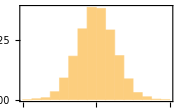

```mathematica
Histogram[Last[fTS[NormalDistribution[0,1],5000,1]],"Knuth","PDF",Frame->True,PlotRange->All,ImageSize->Small]
```

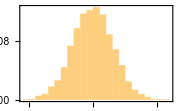

```mathematica
Histogram[Last[fTS[NormalDistribution[0,1],5000,10]],"Knuth","PDF",Frame->True,PlotRange->All,ImageSize->Small]
```

## Mean Deviation and Kappa

```mathematica
fM[dist_, runs_,n_]:=Map[MeanDeviation,fTS[dist,runs, n]];
```

```mathematica
fMLast[dist_, runs_,n_]:=MeanDeviation[fSLast[dist,runs, n]];
```

```mathematica
κ[dist_, runs_,n_,n0_]:=Module[{fMv},
fMv=fM[dist,runs, n];
2-(Log[n]-Log[n0])/(Log[fMv⟦n⟧]-Log[fMv⟦n0⟧])];
```

### Gaussian

#### n=1

```mathematica
Assuming[σ>0,Expectation[x,x\[Distributed]NormalDistribution[0,σ]]]
```

0

```mathematica
Assuming[σ>0,Expectation[Abs[x-0],x\[Distributed]NormalDistribution[0,σ]]]
```

√(2/π) σ

```mathematica
MADGaussian[σ_:1]:=√(2/π)σ;
```

```mathematica
{MADGaussian[],N[MADGaussian[]]}
```

{√(2/π),0.797885}

#### n=2

```mathematica
Assuming[σ>0,Expectation[∑_(j=1)^2 Subscript[x, j],Apply[And,Table[Subscript[x, j]\[Distributed]NormalDistribution[0,σ],{j,1,2}]]]]
```

0

```mathematica
Assuming[σ>0,Expectation[Abs[∑_(j=1)^2 Subscript[x, j]-0],Apply[And,Table[Subscript[x, j]\[Distributed]NormalDistribution[0,σ],{j,1,2}]]]]
```

(2 σ)/(√π)

```mathematica
MADnGaussian[n_,σ_:1]:=√((2n)/π)σ;
```

```mathematica
{MADnGaussian[2],N[MADnGaussian[2]]}
```

{2/(√π),1.12838}

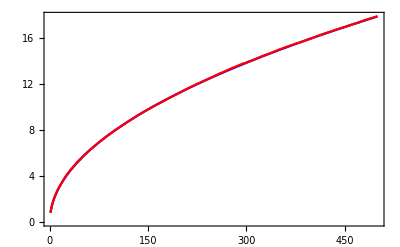

```mathematica
Show[Plot[MADGaussian[1] √n,{n,1,500},Frame->True,PlotStyle->Blue],
ListLinePlot[fM[NormalDistribution[0,1],50000,500],Frame->True,PlotStyle->Red]]
```

```mathematica
Timing[fM[NormalDistribution[0,1],50000,500];]
```

{0.53125,Null}

```mathematica
Timing[fMLast[NormalDistribution[0,1],50000,500]]
```

{0.46875,17.853}

#### Kappa

```mathematica
Grid[Table[{n0,n0+δn,κ[NormalDistribution[0,1],500000,n0+δn,n0]},{n0,{1,2,5,10,20}},{δn,{1,2,5,10,20}}],Frame->All]
```

{1,2,-0.00120661} | {1,3,-0.00165292} | {1,6,0.00374826} | {1,11,0.00246563} | {1,21,0.00130641}
{2,3,-0.000518397} | {2,4,0.0132574} | {2,7,-0.000468393} | {2,12,0.00275827} | {2,22,0.00458112}
{5,6,-0.0138572} | {5,7,0.000988947} | {5,10,0.00194736} | {5,15,-0.00479863} | {5,25,-0.000553435}
{10,11,0.0162351} | {10,12,0.00661287} | {10,15,-0.00187947} | {10,20,0.00292318} | {10,30,0.00607565}
{20,21,0.00794312} | {20,22,0.0109076} | {20,25,0.000759018} | {20,30,0.00421929} | {20,40,-0.00400495}

### StudentT

#### n=1

```mathematica
Assuming[σ>0&&α>1,Expectation[x,x\[Distributed]StudentTDistribution[0,σ,α]]]
```

0

```mathematica
Assuming[σ>0&&α>1,Expectation[Abs[x-0],x\[Distributed]StudentTDistribution[0,σ,α]]]
```

(2 √α σ)/((-1+α) Beta[α/2,1/2])

```mathematica
FunctionExpand[Beta[α/2,1/2]]
```

(√π Gamma[α/2])/Gamma[1/2+α/2]

```mathematica
MADStudentT[α_,σ_:1]:=(2 √α σ Gamma[1/2+α/2])/((α-1) √π Gamma[α/2]);
```

```mathematica
{MADStudentT[3],N[MADStudentT[3]]}
```

{(2 √3)/π,1.10266}

#### n=2

```mathematica
Assuming[σ>0&&α>1,Expectation[∑_(j=1)^2 Subscript[x, j],Apply[And,Table[Subscript[x, j]\[Distributed]StudentTDistribution[0,σ,α],{j,1,2}]]]]
```

0

```mathematica
Expand[Assuming[σ>0&&α>1,Expectation[Abs[∑_(j=1)^2 Subscript[x, j]-0],Apply[And,Table[Subscript[x, j]\[Distributed]StudentTDistribution[0,σ,α],{j,1,2}]]]]]
```

(2^(1-α) √α σ Gamma[1/2 (-1+α)] Gamma[-1/2+α])/Gamma[α/2]^3+(2^(1-α) √α σ Gamma[-1+α] Hypergeometric2F1[1/2,1/2 (-1+α),1-α/2,1])/Gamma[α/2]^2+(2^(1-α) π √α σ Gamma[-1+α] Hypergeometric2F1[1/2,1/2 (-1+α),1-α/2,1])/(Beta[α/2,1/2]^2 Gamma[(1+α)/2]^2)+(2^α √α σ Cos[(π α)/2] Gamma[-1/2+α] Gamma[-α] Hypergeometric2F1[-1/2+α,(1+α)/2,(2+α)/2,1])/(√π Beta[α/2,1/2]^2)+(2^α √α σ Cos[(π α)/2] Gamma[-1/2+α] Gamma[-α] Gamma[(1+α)/2]^2 Hypergeometric2F1[-1/2+α,(1+α)/2,(2+α)/2,1])/(π^(3/2) Gamma[α/2]^2)

About 35 seconds

```mathematica
Expand[Expectation[Abs[∑_(j=1)^2 Subscript[x, j]-0],Apply[And,Table[Subscript[x, j]\[Distributed]StudentTDistribution[0,1,3],{j,1,2}]]]]
```

(3 √3)/π

```mathematica
(2^(1-α) √α σ Gamma[1/2 (-1+α)] Gamma[-1/2+α])/Gamma[α/2]^3//.{α->3,σ->1}
```

(3 √3)/(2 π)

```mathematica
MAD2StudentT[α_,σ_:1]:=(4 √α σ Gamma[-1/2+α/2] Gamma[-1/2+α])/(2^α Gamma[α/2]^3);
```

```mathematica
{MAD2StudentT[3],N[MAD2StudentT[3]]}
```

{(3 √3)/π,1.65399}

#### Different αs

```mathematica
TableForm[N[Map[{#,MADStudentT[#],First[fM[StudentTDistribution[0,1,#],10000000,1]]}&,{100,10,3,2,1.5,1.25,1.1}]]]
```

100. | 0.803932 | 0.803991
10. | 0.864685 | 0.864908
3. | 1.10266 | 1.10268
2. | 1.41421 | 1.41563
1.5 | 2.04441 | 2.02686
1.25 | 3.31281 | 3.19702
1.1 | 7.12877 | 5.86383

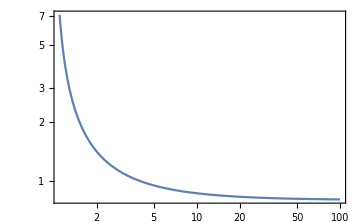

```mathematica
LogLogPlot[MADStudentT[α],{α,1.1,100},Frame->True,ImageSize->Medium,PlotRange->All]
```

```mathematica
TableForm[N[Map[{#,MAD2StudentT[#],Last[fM[StudentTDistribution[0,1,#],10000000,2]]}&,{100,10,3,2,1.5,1.25,1.1}]]]
```

100. | 1.13837 | 1.13821
10. | 1.23989 | 1.23935
3. | 1.65399 | 1.65435
2. | 2.22144 | 2.22182
1.5 | 3.41264 | 3.44544
1.25 | 5.88051 | 5.74717
1.1 | 13.4437 | 10.6285

```mathematica
approxgamma[α_,γ_,n_]:={{α,n,γ},Table[(j^γ)MADStudentT[α],{j,1,n}]};
```

```mathematica
tblmadStudT[α_,n_,runs_:10000,σ_:1]:={runs,fM[StudentTDistribution[0,σ,α],runs,n]};
```

```mathematica
plotmadStudT[{runs_,results_},{{α_,n_,γ_},simuls_}]:=
ListPlot[{simuls,results},PlotStyle->{Blue,Red},ImageSize->Medium,PlotLegends->{"Approximated","Simulated"},Frame->True,AxesOrigin->{1,0},Joined->{True,False},PlotMarkers->{None,{Automatic, 5}},Filling->None,PlotRange->{{1,n},All},PlotLabel->"MAD Sum[n x StudentT(α="<>ToString[α]<>")] γ="<>ToString[γ]<>" runs: "<>ToString[runs]];
```

```mathematica
Timing[resultsStT100=tblmadStudT[100,20]]
```

{0.032404,{10000,{0.796961,1.13242,1.39511,1.61637,1.80629,1.98142,2.12829,2.29443,2.44771,2.58851,2.69969,2.827,2.93592,3.04363,3.13871,3.2475,3.33838,3.43038,3.51157,3.62537}}}

```mathematica
approxStT100=approxgamma[100,0.5,20]
```

{{100,20,0.5},{0.803932,1.13693,1.39245,1.60786,1.79765,1.96922,2.127,2.27386,2.4118,2.54226,2.66634,2.7849,2.89862,3.00804,3.11361,3.21573,3.3147,3.41079,3.50426,3.59529}}

```mathematica
n=20;
```

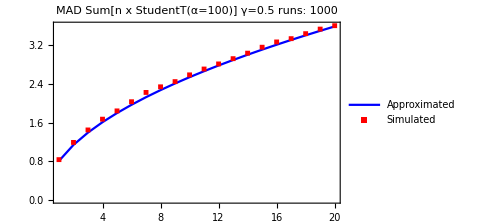

```mathematica
α=100;γ=0.5;runs=1000;
plotmadStudT[tblmadStudT[α,n,runs],approxgamma[α,γ,n]]
```

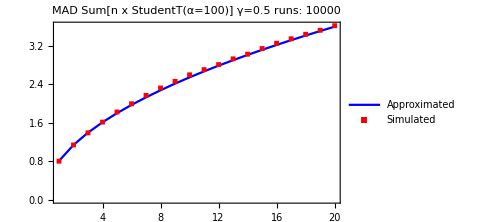

```mathematica
α=100;γ=0.5;
plotmadStudT[tblmadStudT[α,n],approxgamma[α,γ,n]]
```

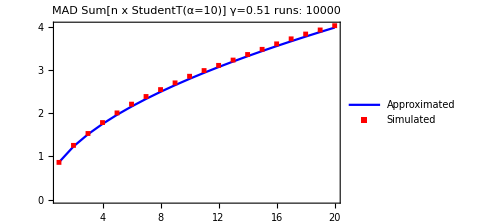

```mathematica
α=10;γ=0.51;
plotmadStudT[tblmadStudT[α,n],approxgamma[α,γ,n]]
```

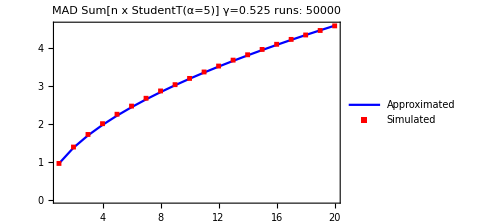

```mathematica
α=5;γ=0.525;runs=50000;
plotmadStudT[tblmadStudT[α,n,runs],approxgamma[α,γ,n]]
```

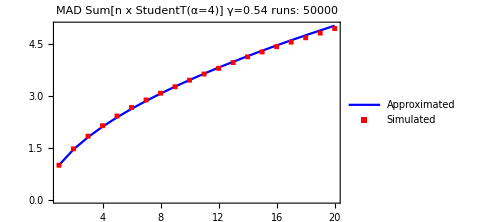

```mathematica
α=4;γ=0.54;runs=50000;
plotmadStudT[tblmadStudT[α,n,runs],approxgamma[α,γ,n]]
```

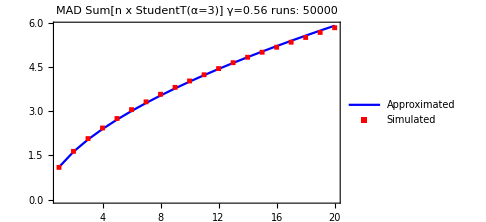

```mathematica
α=3;γ=0.56;runs=50000;
plotmadStudT[tblmadStudT[α,n,runs],approxgamma[α,γ,n]]
```

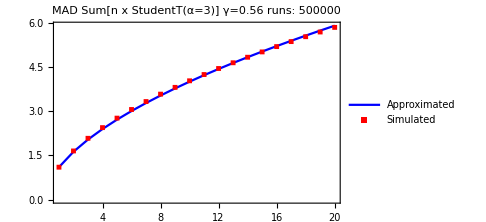

```mathematica
α=3;γ=0.56;runs=500000;
plotmadStudT[tblmadStudT[α,n,runs],approxgamma[α,γ,n]]
```

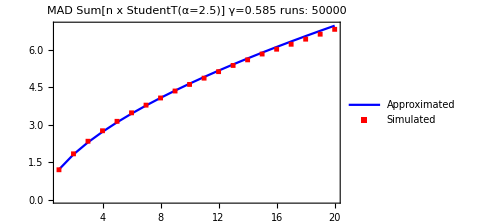

```mathematica
α=2.5;γ=0.585;runs=50000;
plotmadStudT[tblmadStudT[α,n,runs],approxgamma[α,γ,n]]
```

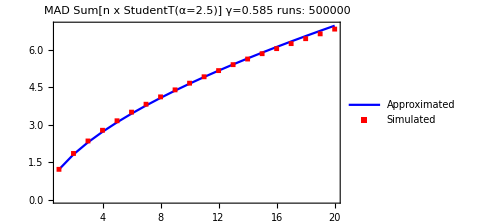

```mathematica
α=2.5;γ=0.585;runs=500000;
plotmadStudT[tblmadStudT[α,n,runs],approxgamma[α,γ,n]]
```

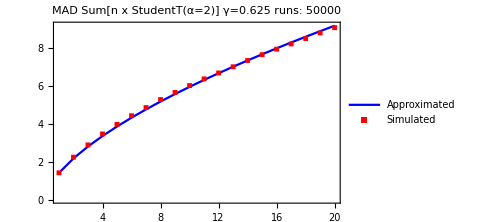

```mathematica
α=2;γ=0.625;runs=50000;
plotmadStudT[tblmadStudT[α,n,runs],approxgamma[α,γ,n]]
```

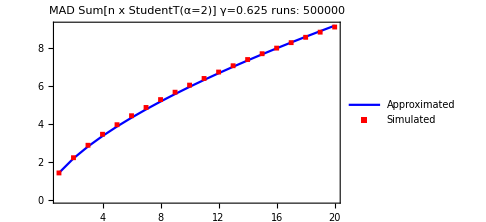

```mathematica
α=2;γ=0.625;runs=500000;
plotmadStudT[tblmadStudT[α,n,runs],approxgamma[α,γ,n]]
```

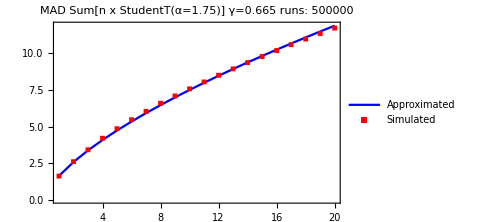

```mathematica
α=1.75;γ=0.665;runs=500000;
plotmadStudT[tblmadStudT[α,n,runs],approxgamma[α,γ,n]]
```

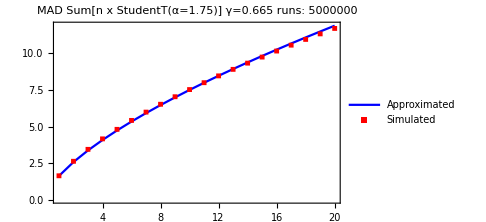

```mathematica
α=1.75;γ=0.665;runs=5000000;
plotmadStudT[tblmadStudT[α,n,runs],approxgamma[α,γ,n]]
```

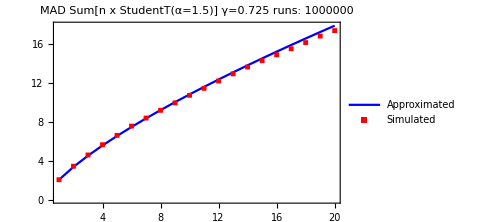

```mathematica
α=1.5;γ=0.725;runs=1000000;
plotmadStudT[tblmadStudT[α,n,runs],approxgamma[α,γ,n]]
```

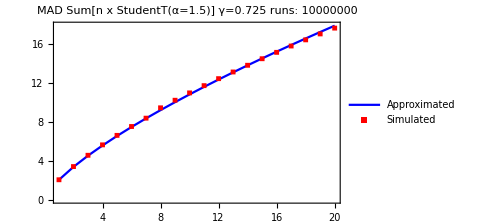

```mathematica
α=1.5;γ=0.725;runs=10000000;
plotmadStudT[tblmadStudT[α,n,runs],approxgamma[α,γ,n]]
```

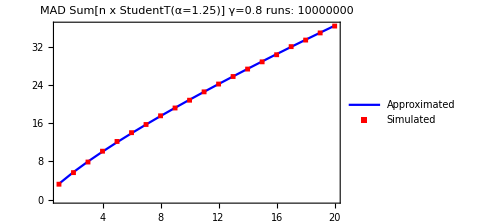

```mathematica
α=1.25;γ=0.8;runs=10000000;
plotmadStudT[tblmadStudT[α,n,runs],approxgamma[α,γ,n]]
```

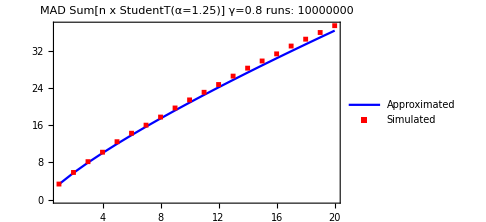

```mathematica
α=1.25;γ=0.8;runs=10000000;
plotmadStudT[tblmadStudT[α,n,runs],approxgamma[α,γ,n]]
```

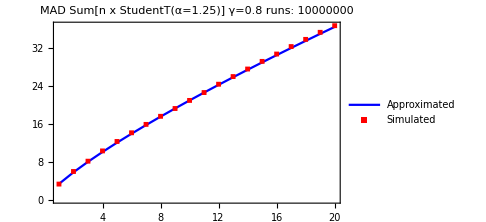

```mathematica
α=1.25;γ=0.8;runs=10000000;
plotmadStudT[tblmadStudT[α,n,runs],approxgamma[α,γ,n]]
```

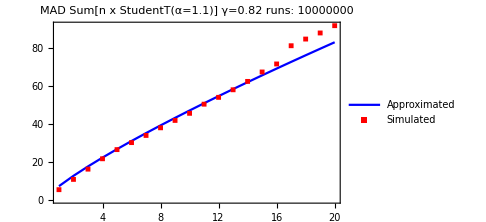

```mathematica
α=1.1;γ=0.82;runs=10000000;
plotmadStudT[tblmadStudT[α,n,runs],approxgamma[α,γ,n]]
```

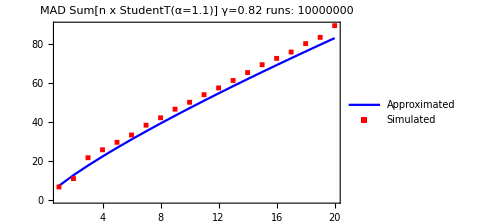

```mathematica
α=1.1;γ=0.82;runs=10000000;
plotmadStudT[tblmadStudT[α,n,runs],approxgamma[α,γ,n]]
```

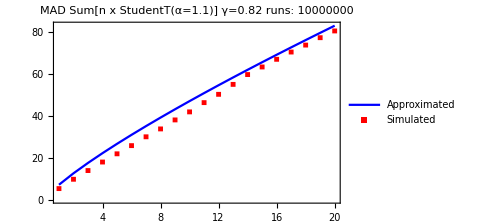

```mathematica
α=1.1;γ=0.82;runs=10000000;
plotmadStudT[tblmadStudT[α,n,runs],approxgamma[α,γ,n]]
```

```mathematica
data={{10,0.51},{5,0.525},{4,0.54},{3,0.56},{2.5,0.585},{2,0.625},{1.5,0.725},{1.25,0.8},{1.1,0.82}};
```

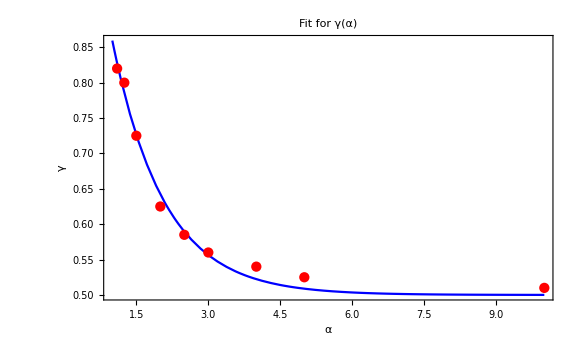

```mathematica
Show[Plot[1/2+2^(-1.336α-0.14),{α,1,10},PlotRange->All,Frame->True,ImageSize->Large,PlotStyle->Blue,FrameLabel->{"α","γ"},PlotLabel->"Fit for γ(α)"],
ListPlot[data,PlotStyle->Red]]
```

```mathematica
FindFit[data,1/2+2^(a x+b),{a,b},x]
```

{a→-1.33628,b→-0.143495}

#### Kappa

```mathematica
κ1nStT3[n_]:=2-Log[n]/Log[(ⅇ/n)^n Gamma[n+1,n]-1];
```

```mathematica
Grid[Table[{n0,n0+δn,κ[StudentTDistribution[0,1,100],500000,n0+δn,n0]},{n0,{1,2,5,10,20}},{δn,{1,2,5,10,20}}],Frame->All]
```

{1,2,0.0126674} | {1,3,0.00544291} | {1,6,0.00160482} | {1,11,0.00234111} | {1,21,0.00357128}
{2,3,-0.00259367} | {2,4,-7.18106×10^-6} | {2,7,0.00262718} | {2,12,0.00246897} | {2,22,0.00400433}
{5,6,-0.00304048} | {5,7,-0.00380651} | {5,10,0.000187082} | {5,15,-0.00715996} | {5,25,-0.0000627475}
{10,11,-0.0189071} | {10,12,0.00124208} | {10,15,-0.0131058} | {10,20,0.00984608} | {10,30,0.00628774}
{20,21,-0.0450936} | {20,22,-0.00777931} | {20,25,-0.0242879} | {20,30,0.00976923} | {20,40,0.00786511}

```mathematica
Grid[Table[{n0,n0+δn,κ[StudentTDistribution[0,1,3],500000,n0+δn,n0]},{n0,{1,2,5,10,30,100}},{δn,{1,2,5,10,30,100}}],Frame->All]
```

{1,2,0.292633} | {1,3,0.265074} | {1,6,0.243411} | {1,11,0.21671} | {1,31,0.189776} | {1,101,0.15971}
{2,3,0.234284} | {2,4,0.21932} | {2,7,0.213619} | {2,12,0.192242} | {2,32,0.164866} | {2,102,0.132186}
{5,6,0.181745} | {5,7,0.17047} | {5,10,0.159591} | {5,15,0.150052} | {5,35,0.129084} | {5,105,0.107721}
{10,11,0.15787} | {10,12,0.114892} | {10,15,0.128356} | {10,20,0.125679} | {10,40,0.103175} | {10,110,0.0893753}
{30,31,0.0930356} | {30,32,0.0724145} | {30,35,0.106017} | {30,40,0.0784087} | {30,60,0.0778231} | {30,130,0.0650391}
{100,101,0.036312} | {100,102,0.00705677} | {100,105,0.0413458} | {100,110,0.0534601} | {100,130,0.05125} | {100,200,0.0442501}

```mathematica
Grid[Table[{n0,n0+δn,κ[StudentTDistribution[0,1,2],5000000,n0+δn,n0]},{n0,{1,2,5,10,30,100}},{δn,{1,2,5,10,30,100}}],Frame->All]
```

{1,2,0.469116} | {1,3,0.451458} | {1,6,0.425944} | {1,11,0.408595} | {1,31,0.378809} | {1,101,0.350945}
{2,3,0.420495} | {2,4,0.418573} | {2,7,0.399021} | {2,12,0.38279} | {2,32,0.354538} | {2,102,0.326709}
{5,6,0.378625} | {5,7,0.365963} | {5,10,0.355443} | {5,15,0.346123} | {5,35,0.325522} | {5,105,0.303171}
{10,11,0.326519} | {10,12,0.333365} | {10,15,0.329503} | {10,20,0.325572} | {10,40,0.303725} | {10,110,0.285532}
{30,31,0.291116} | {30,32,0.278869} | {30,35,0.282786} | {30,40,0.278694} | {30,60,0.274462} | {30,130,0.258893}
{100,101,0.214062} | {100,102,0.219247} | {100,105,0.222882} | {100,110,0.236205} | {100,130,0.230878} | {100,200,0.231414}

```mathematica
Grid[Table[{n0,n0+δn,κ[StudentTDistribution[0,1,1.25],5000000,n0+δn,n0]},{n0,{1,2,5,10,30,100}},{δn,{1,2,5,10,30,100}}],Frame->All]
```

{1,2,0.860039} | {1,3,0.821536} | {1,6,0.751645} | {1,11,0.787415} | {1,31,0.726556} | {1,101,0.742925}
{2,3,0.770185} | {2,4,0.757985} | {2,7,0.803018} | {2,12,0.774587} | {2,32,0.762677} | {2,102,0.770758}
{5,6,0.700449} | {5,7,0.74998} | {5,10,0.809757} | {5,15,0.777834} | {5,35,0.750315} | {5,105,0.747099}
{10,11,0.845897} | {10,12,1.00048} | {10,15,0.774199} | {10,20,0.688933} | {10,40,0.770301} | {10,110,0.773162}
{30,31,0.632362} | {30,32,0.754267} | {30,35,0.74742} | {30,40,0.778662} | {30,60,0.735688} | {30,130,0.757601}
{100,101,0.309682} | {100,102,0.603276} | {100,105,0.697752} | {100,110,0.868923} | {100,130,0.745961} | {100,200,0.764921}

10 minutes

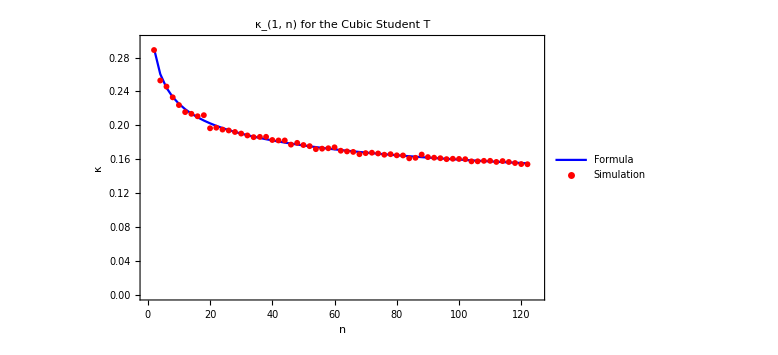

```mathematica
DiscretePlot[{κ1nStT3[n],κ[StudentTDistribution[0,1,3],500000,n,1]},{n,2,122,2},Frame->True,PlotRange->{{0,125},{0,0.30}},PlotStyle->{Blue,Red},
PlotLegends->{"Formula", "Simulation"},ImageSize->Large,Joined->{True,False},Filling->None,PlotLabel->"κ_(1, n) for the Cubic Student T",FrameLabel->{"n","κ"}]
```

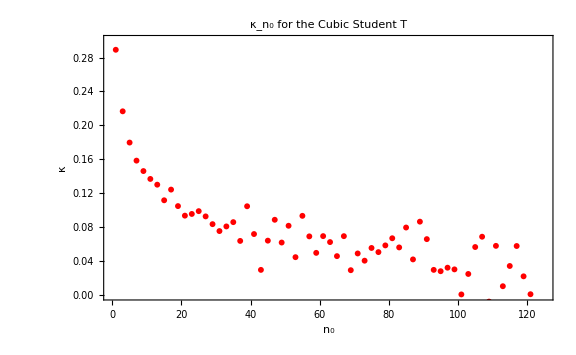

```mathematica
DiscretePlot[κ[StudentTDistribution[0,1,3],5000000,n0+1,n0],{n0,1,121,2},Frame->True,PlotRange->{{0,125},{0,0.30}},PlotStyle->{Red},
ImageSize->Large,Joined->{False},Filling->None,PlotLabel->"κ_n_0 for the Cubic Student T",FrameLabel->{"n_0","κ"}]
```

```mathematica
Timing[κ10tbl=Flatten[Table[{n,κ[StudentTDistribution[0,1,10],5000,n,1]},{n,2,122,10},500],1];]
```

{1052.63,Null}

```mathematica
SmoothHistogram3D[κ10tbl,ImageSize->Large,AxesLabel->{"n","κ_(1, n)"},ColorFunction->"TemperatureMap",PlotLabel->"Distribution of κ_(1, n) for α=10",PlotRange->{{0,125},{-0.05,0.15},All}]
```

-Graphics3D-

```mathematica
Timing[κ3tbl=Flatten[Table[{n,κ[StudentTDistribution[0,1,3],5000,n,1]},{n,2,122,10},500],1];]
```

{1063.77,Null}

```mathematica
SmoothHistogram3D[κ3tbl,ImageSize->Large,AxesLabel->{"n","κ_(1, n)"},ColorFunction->"TemperatureMap",PlotLabel->"Distribution of κ_(1, n) for α=3",PlotRange->{{0,125},{0.05,0.4},All}]
```

-Graphics3D-

```mathematica
Timing[κP3tbl=Flatten[Table[{n,κ[ParetoDistribution[1,3],5000,n,1]},{n,2,122,10},500],1];]
```

{378.254,Null}

```mathematica
SmoothHistogram3D[κP3tbl,ImageSize->Large,AxesLabel->{"n","κ_(1, n)"},ColorFunction->"TemperatureMap",PlotLabel->"Distribution of κ_(1, n) for Pareto(3)",PlotRange->{{0,125},{0.2,0.5},All}]
```

-Graphics3D-

```mathematica
Timing[κ2tbl=Flatten[Table[{n,κ[StudentTDistribution[0,1,2],5000,n,1]},{n,2,122,10},500],1];]
```

{1109.07,Null}

```mathematica
SmoothHistogram3D[κ2tbl,ImageSize->Large,AxesLabel->{"n","κ_(1, n)"},ColorFunction->"TemperatureMap",PlotLabel->"Distribution of κ_(1, n) for α=2",PlotRange->{{0,125},{0.2,0.5},All}]
```

-Graphics3D-

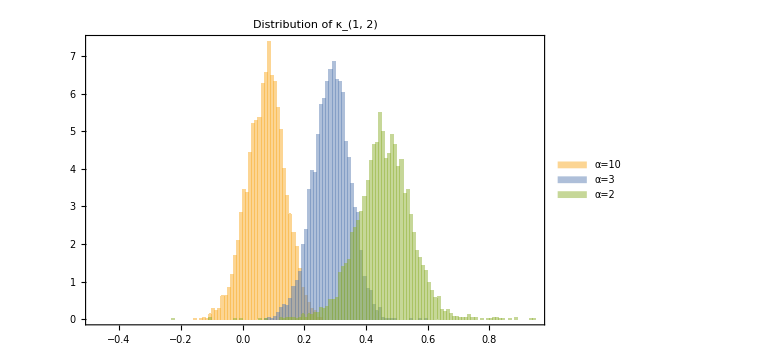

```mathematica
Histogram[{
Table[κ[StudentTDistribution[0,1,10],5000,2,1],5000],
Table[κ[StudentTDistribution[0,1,3],5000,2,1],5000],
Table[κ[StudentTDistribution[0,1,2],5000,2,1],5000]},
{0.01},"PDF",Frame->True,ChartLegends->{"α=10","α=3","α=2"},
ImageSize->Large,PlotLabel->"Distribution of κ_(1, 2)"]
```

```mathematica
PairedHistogram[
Labeled[Table[κ[StudentTDistribution[0,1,2],5000,2,1],5000],"StudentT, α=2"],
Labeled[Table[κ[ParetoDistribution[1,3],5000,2,1],5000],"Pareto, α=3"],
{Range[0,1,0.01]},"PDF",ImageSize->Large,PlotLabel->"Distribution of κ_(1, 2)"]
```

-Graphics-

### LogNormal

#### n=1

```mathematica
Assuming[σ>0&&μ>=0,Expectation[x,x\[Distributed]LogNormalDistribution[μ,σ]]]
```

ⅇ^(μ+σ^2/2)

```mathematica
Assuming[σ>0&&μ>=0,Expectation[Abs[x-ⅇ^(μ+σ^2/2)],x\[Distributed]LogNormalDistribution[μ,σ]]]
```

2 ⅇ^(μ+σ^2/2) Erf[σ/(2 √2)]

```mathematica
MADLogNormal[μ_,σ_]:=2 ⅇ^(μ+σ^2/2)Erf[σ/(2 √2)];
```

```mathematica
{MADLogNormal[0,1],N[MADLogNormal[0,1]]}
```

{2 √ⅇ Erf[1/(2 √2)],1.26267}

#### n=2

```mathematica
Assuming[σ>0&&μ>=0,Expectation[∑_(j=1)^2 Subscript[x, j],Apply[And,Table[Subscript[x, j]\[Distributed]LogNormalDistribution[μ,σ],{j,1,2}]]]]
```

2 ⅇ^(μ+σ^2/2)

```mathematica
Assuming[σ>0&&μ>=0,Expectation[Abs[∑_(j=1)^2 Subscript[x, j]-2 ⅇ^(μ+σ^2/2)],Apply[And,Table[Subscript[x, j]\[Distributed]LogNormalDistribution[μ,σ],{j,1,2}]]]]
```

Expectation[Abs[-2 ⅇ^(μ+σ^2/2)+x_1+x_2],x_1\[Distributed]LogNormalDistribution[μ,σ]&&x_2\[Distributed]LogNormalDistribution[μ,σ]]

```mathematica
Assuming[σ>0,Expectation[Abs[∑_(j=1)^2 Subscript[x, j]-2 ⅇ^(σ^2/2)],Apply[And,Table[Subscript[x, j]\[Distributed]LogNormalDistribution[0,σ],{j,1,2}]]]]
```

Expectation[Abs[-2 ⅇ^(σ^2/2)+x_1+x_2],x_1\[Distributed]LogNormalDistribution[0,σ]&&x_2\[Distributed]LogNormalDistribution[0,σ]]

#### Kappa

```mathematica
Grid[Table[{n0,n0+δn,κ[LogNormalDistribution[0,0.1],500000,n0+δn,n0]},{n0,{1,2,5,10,20}},{δn,{1,2,5,10,20}}],Frame->All]
```

{1,2,0.0140428} | {1,3,0.00971792} | {1,6,0.00250126} | {1,11,-0.0000120344} | {1,21,0.00383428}
{2,3,0.00612279} | {2,4,-0.00985255} | {2,7,0.00809889} | {2,12,0.00316236} | {2,22,0.00374518}
{5,6,0.0033146} | {5,7,-0.0104056} | {5,10,0.0136543} | {5,15,-0.000139651} | {5,25,0.00759066}
{10,11,-0.00806948} | {10,12,0.00135656} | {10,15,-0.00548156} | {10,20,0.00148457} | {10,30,0.00965574}
{20,21,-0.0351883} | {20,22,-0.0185077} | {20,25,-0.0172528} | {20,30,-0.00445108} | {20,40,0.00962739}

```mathematica
Grid[Table[{n0,n0+δn,κ[LogNormalDistribution[0,0.5],500000,n0+δn,n0]},{n0,{1,2,5,10,20}},{δn,{1,2,5,10,20}}],Frame->All]
```

{1,2,0.179097} | {1,3,0.147275} | {1,6,0.121643} | {1,11,0.102649} | {1,21,0.0840184}
{2,3,0.118905} | {2,4,0.103204} | {2,7,0.0821345} | {2,12,0.0717586} | {2,22,0.0578058}
{5,6,0.0292264} | {5,7,0.0386431} | {5,10,0.0563777} | {5,15,0.0459193} | {5,25,0.0350671}
{10,11,0.0116263} | {10,12,0.0301011} | {10,15,0.0387334} | {10,20,0.033863} | {10,30,0.0271725}
{20,21,0.0153674} | {20,22,0.0537896} | {20,25,0.0166888} | {20,30,0.00984616} | {20,40,0.0155336}

```mathematica
Grid[Table[{n0,n0+δn,κ[LogNormalDistribution[0,3],5000000,n0+δn,n0]},{n0,{1,2,5,10,20}},{δn,{1,2,5,10,20}}],Frame->All]
```

{1,2,0.915036} | {1,3,0.908234} | {1,6,0.88399} | {1,11,0.872416} | {1,21,0.875809}
{2,3,0.874688} | {2,4,0.885959} | {2,7,0.907682} | {2,12,0.877468} | {2,22,0.845554}
{5,6,0.856874} | {5,7,0.786707} | {5,10,0.915788} | {5,15,0.865076} | {5,25,0.82873}
{10,11,0.840716} | {10,12,0.805075} | {10,15,0.853188} | {10,20,0.850154} | {10,30,0.811435}
{20,21,0.805881} | {20,22,0.77915} | {20,25,0.788007} | {20,30,0.764093} | {20,40,0.796693}

```mathematica
κ1LN[n_,σ_]:=2-Log[n]/Log[n Erf[(√Log[(n+ⅇ^(σ^2)-1)/n])/(2 √2)]/Erf[σ/(2 √2)]];
```

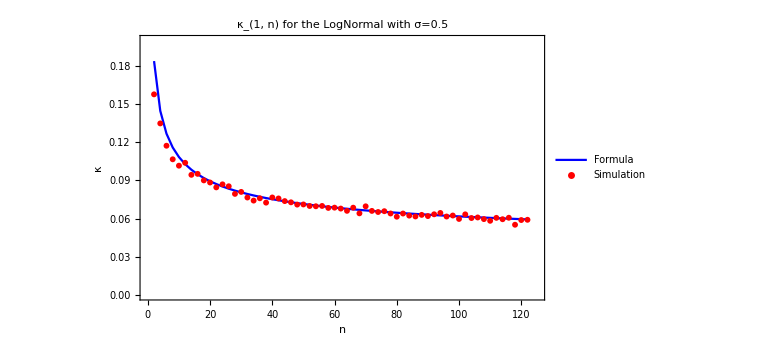

```mathematica
DiscretePlot[{κ1LN[n,0.5],κ[LogNormalDistribution[0,0.5],500000,n,1]},{n,2,122,2},Frame->True,PlotRange->{{0,125},{0,0.20}},PlotStyle->{Blue,Red},
PlotLegends->{"Formula", "Simulation"},ImageSize->Large,Joined->{True,False},Filling->None,PlotLabel->"κ_(1, n) for the LogNormal with σ=0.5",FrameLabel->{"n","κ"}]
```

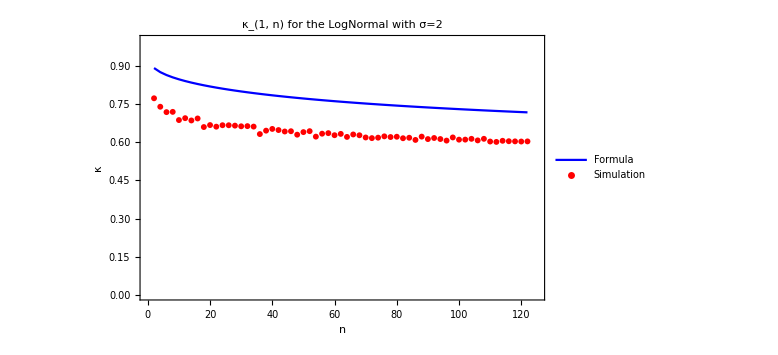

```mathematica
DiscretePlot[{κ1LN[n,2],κ[LogNormalDistribution[0,2],500000,n,1]},{n,2,122,2},Frame->True,PlotRange->{{0,125},{0,1}},PlotStyle->{Blue,Red},
PlotLegends->{"Formula", "Simulation"},ImageSize->Large,Joined->{True,False},Filling->None,PlotLabel->"κ_(1, n) for the LogNormal with σ=2",FrameLabel->{"n","κ"}]
```

### Pareto

```mathematica
Assuming[α>1,Expectation[x,x\[Distributed]ParetoDistribution[L,α]]]
```

(L α)/(-1+α)

```mathematica
Assuming[L>0&&α>1,Expectation[Abs[x-(L α)/(-1+α)],x\[Distributed]ParetoDistribution[L,α]]]
```

2 L (-1+α)^(-2+α) α^(1-α)

```mathematica
MADPareto[α_,L_]:=2 L (-1+α)^(-2+α) α^(1-α);
```

```mathematica
{MADPareto[2,1],N[MADPareto[2,1]]}
```

{1,1.}

```mathematica
Assuming[α>1,TransformedDistribution[ⅇ^x,x\[Distributed]ParetoDistribution[L,α]]]
```

TransformedDistribution[ⅇ^x,x\[Distributed]ParetoDistribution[L,α]]

```mathematica
Assuming[α>1,Expectation[ⅇ^x,x\[Distributed]ParetoDistribution[L,α]]]
```

α ExpIntegralE[1+α,-L]

### Simulations

```mathematica
plotfMs[dists_,runs_,n_]:=ListLinePlot[Map[fM[#,runs,n]&,dists],Frame->True,PlotRange->{{1,Automatic},Automatic},PlotMarkers->{Automatic, 10},ImageSize->Medium,PlotLabel->"𝔼|Sn=X1+X2+...+Xn| for several dists",PlotLegends->dists];
```

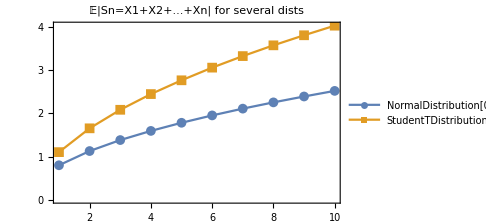

```mathematica
plotfMs[{NormalDistribution[0,1],StudentTDistribution[0,1,3]},1000000,10]
```

```mathematica
TableForm[N[Map[{#,MAD2StudentT[#],Last[fM[StudentTDistribution[0,1,#],10000000,2]]}&,{100,10,3,2,1.5,1.25,1.1}]]]
```

100. | 1.13837 | 1.13906
10. | 1.23989 | 1.23906
3. | 1.65399 | 1.65364
2. | 2.22144 | 2.2216
1.5 | 3.41264 | 3.39506
1.25 | 5.88051 | 5.78691
1.1 | 13.4437 | 10.2681

```mathematica
TableForm[N[Map[{#,MADLogNormal[0,#],First[fM[LogNormalDistribution[0,#],10000000,1]]}&,{0.1,0.25,0.5,1,1.5,2,2.5,3}]]]
```

0.1 | 0.080155 | 0.0801747
0.25 | 0.205268 | 0.20537
0.5 | 0.447396 | 0.447359
1. | 1.26267 | 1.26242
1.5 | 3.36819 | 3.36684
2. | 10.0889 | 10.0646
2.5 | 35.9015 | 36.1061
3. | 155.979 | 158.029

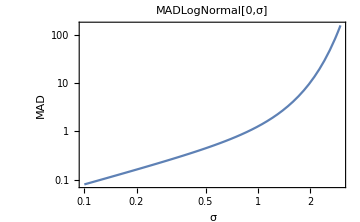

```mathematica
LogLogPlot[MADLogNormal[0,σ],{σ,0.1,3},Frame->True,ImageSize->Medium,PlotRange->All,PlotLabel->"MADLogNormal[0,σ]",FrameLabel->{"σ","MAD"}]
```

```mathematica
TableForm[N[Map[{#,MADPareto[#,1],First[fM[ParetoDistribution[1,#],10000000,1]]}&,{100,10,3,2,1.5,1.25,1.1}]]]
```

100. | 0.00746929 | 0.00746932
10. | 0.0860934 | 0.0861695
3. | 0.444444 | 0.445248
2. | 1. | 1.00002
1.5 | 2.3094 | 2.26589
1.25 | 5.34992 | 5.05522
1.1 | 15.7359 | 11.1727

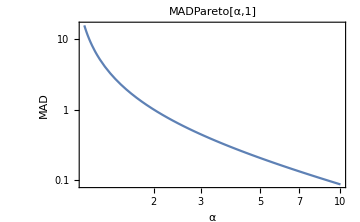

```mathematica
LogLogPlot[MADPareto[α,1],{α,1.1,10},Frame->True,ImageSize->Medium,PlotRange->All,PlotLabel->"MADPareto[α,1]",FrameLabel->{"α","MAD"}]
```

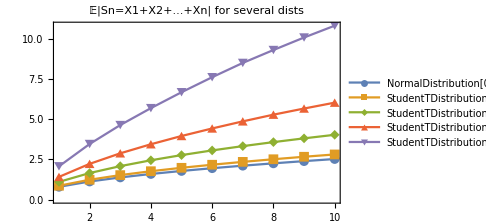

```mathematica
plotfMs[{NormalDistribution[0,1],StudentTDistribution[0,1,10],StudentTDistribution[0,1,3],StudentTDistribution[0,1,2],StudentTDistribution[0,1,1.5]},1000000,10]
```

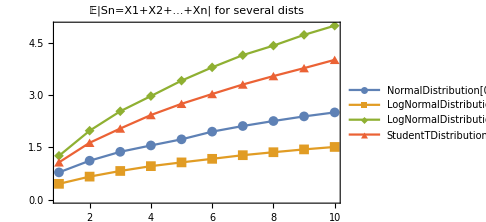

```mathematica
plotfMs[{
NormalDistribution[0,1],
LogNormalDistribution[0,0.5],
LogNormalDistribution[0,1],
StudentTDistribution[0,1,3]
},5000,10]
```

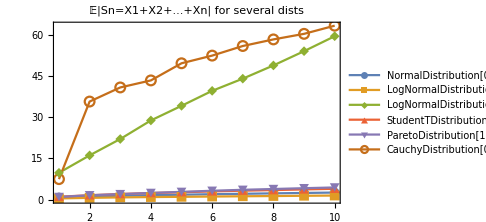

```mathematica
plotfMs[{
NormalDistribution[0,1],
LogNormalDistribution[0,0.5],
LogNormalDistribution[0,2],
StudentTDistribution[0,1,3],
ParetoDistribution[1,2],
CauchyDistribution[0,1]
},5000,10]
```

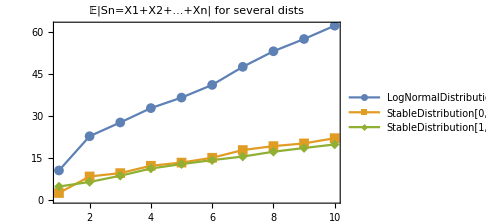

```mathematica
plotfMs[{
LogNormalDistribution[0,2],
StableDistribution[0,1.2,0,0,1],
StableDistribution[1,1.2,0,0,1]
},5000,10]
```